# Ph3 Set 4

## Jacob Snyder

## 4/4/19

```mathematica
data=Rest@Import["http://pmaweb.caltech.edu/~phy003/labs/Data1.txt","TSV"]
```

{{0.,3.4039},{0.5,3.9881},{1.,4.2004},{1.5,5.0291},{2.,5.188},{2.5,5.3914},{3.,5.7904},{3.5,5.4771},{4.,5.784},{4.5,5.9271},{5.,7.1422},{5.5,7.1213},{6.,6.8499},{6.5,7.936},{7.,8.3686},{7.5,8.2178},{8.,8.8891},{8.5,8.8176},{9.,8.8702},{9.5,9.8769},{10.,9.7354}}

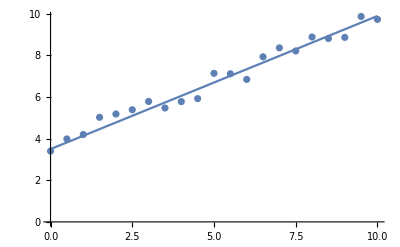

```mathematica
Show[ListPlot[data],Plot[0.64x+3.5,{x,0,10}]]
```

```mathematica
lsq=Fit[data,{1,x},x]
lsq=LinearModelFit[data,{1,x},x]
```

3.6771+0.617003 x

FittedModel[3.6771+0.617003 x]

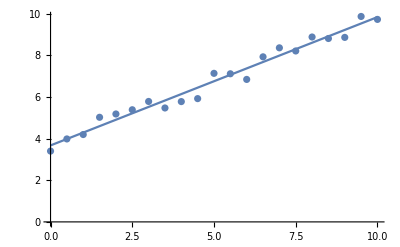

```mathematica
Show[ListPlot[data],Plot[lsq,{x,0,10}]]
```

```mathematica
data2=Import["http://pmaweb.caltech.edu/~phy003/labs/LorentzianData.txt","TSV"]
```

{{-2.,0.26},{-1.9,0.69},{-1.8,0.4},{-1.7,0.86},{-1.6,0.72},{-1.5,0.54},{-1.4,0.52},{-1.3,0.68},{-1.2,0.96},{-1.1,0.73},{-1.,1.06},{-0.9,1.17},{-0.8,1.04},{-0.7,1.},{-0.6,1.19},{-0.5,1.65},{-0.4,1.34},{-0.3,1.9},{-0.2,1.75},{-0.1,1.64},{0.,1.72},{0.1,1.98},{0.2,1.75},{0.3,1.99},{0.4,2.19},{0.5,2.45},{0.6,2.28},{0.7,2.08},{0.8,2.1},{0.9,2.13},{1.,1.79},{1.1,1.7},{1.2,1.85},{1.3,1.9},{1.4,1.94},{1.5,1.72},{1.6,1.43},{1.7,1.23},{1.8,1.56},{1.9,1.16},{2.,1.25}}

```mathematica
Clear[a,c,w]
fit=NonlinearModelFit[data2,a/(1+((x-c)/w)^2),{{a,2.5},{c,1},{w,1}},x]
```

FittedModel[2.16987/(1+0.467867 (-«19»+x)^2)]

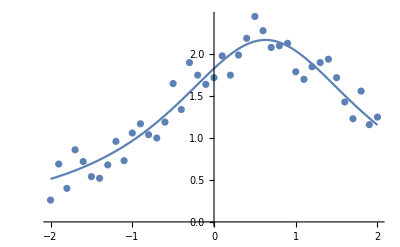

```mathematica
Show[ListPlot[data2],Plot[fit[x],{x,-2,2}]]
```

```mathematica
fit["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 2.16987 | 0.0552674 | 39.2612 | 2.28309×10^-32
c | 0.630755 | 0.0398011 | 15.8477 | 2.47027×10^-18
w | 1.46197 | 0.0729791 | 20.0327 | 8.53186×10^-22

```mathematica
fit["BestFit"]
```

2.16987/(1+0.467867 (-0.630755+x)^2)

```mathematica
residuals1=Table[data2[[i,2]]-fit[data2[[i,1]]],{i,Length[data2]}]
```

{-0.251997,0.147066,-0.176414,0.247329,0.0680423,-0.154541,-0.220703,-0.110733,0.11508,-0.173546,0.0931344,0.134912,-0.0683461,-0.18666,-0.0798895,0.292321,-0.109392,0.355957,0.109765,-0.0961127,-0.109349,0.062815,-0.246542,-0.0742123,0.0728765,0.297352,0.111093,-0.0850102,-0.041172,0.0313143,-0.249751,-0.267205,-0.0342065,0.106058,0.240616,0.116865,-0.0773423,-0.183681,0.236618,-0.0772891,0.0940773}

```mathematica
Needs["ErrorBarPlots`"]
```

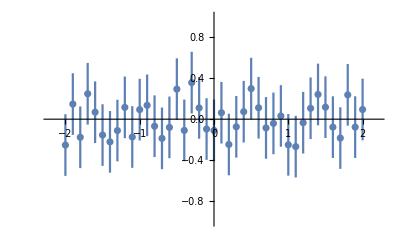

```mathematica
ErrorListPlot[Table[{{data2[[i,1]],residuals1[[i]]},ErrorBar[0.3]},{i,Length[residuals1]}],PlotRange->{{-2.2,2.2},{-1,1}}]
```

The residual plots satisfy the criteria specified in the problem. The error bars appear to have been chosen correctly.

```mathematica
residuals2=Table[data[[i,2]]-lsq[data[[i,1]]],{i,Length[data]}]
```

{-0.273203,0.00249498,-0.0937066,0.426492,0.27689,0.171789,0.262287,-0.359514,-0.361116,-0.526517,0.380081,0.0506794,-0.529222,0.248376,0.372475,-0.0868268,0.275972,-0.10403,-0.359932,0.338267,-0.111735}

```mathematica
Needs["ErrorBarPlots`"]
```

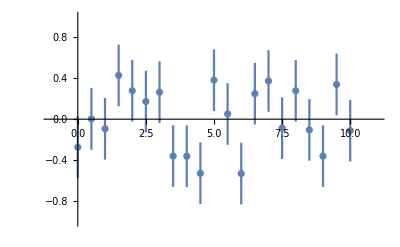

```mathematica
ErrorListPlot[Table[{{data[[i,1]],residuals2[[i]]},ErrorBar[0.3]},{i,Length[residuals2]}],PlotRange->{{-1,11},{-1, 1}}]
```

The residual plots satisfy the criteria specified in the problem. The error bars appear to have been chosen correctly.